```mathematica
"definição do retângulo"
a=1
b=1
```

definição do retângulo

1

1

```mathematica
"definição da base utilizada"
φ[x_,y_,n_,m_]=Sin[π*n(x/a)]Sin[π*m(y/b)]
nM=2
mM=2
Base[x_,y_]=Table[φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM],{i,0,nM*mM-1}]
```

definição da base utilizada

Sin[n π x] Sin[m π y]

2

2

{Sin[π x] Sin[π y],Sin[2 π x] Sin[π y],Sin[π x] Sin[2 π y],Sin[2 π x] Sin[2 π y]}

```mathematica
"definição da matriz A"
A[k_] = Table[∫_0^b ∫_0^a φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]Laplacian[φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM],{x,y}]ⅆxⅆy+k^2∫_0^b ∫_0^a φ[x,y,1+Mod[i,nM],1+(i-Mod[i,nM])/mM]φ[x,y,1+Mod[j,nM],1+(j-Mod[j,nM])/mM]ⅆxⅆy ,{i,0,nM*mM-1},{j,0,nM*mM-1}]
A[k] // MatrixForm
```

definição da matriz A

{{k^2/4-π^2/2,0,0,0},{0,k^2/4-(5 π^2)/4,0,0},{0,0,k^2/4-(5 π^2)/4,0},{0,0,0,k^2/4-2 π^2}}

(k^2/4-π^2/2 | 0 | 0 | 0
0 | k^2/4-(5 π^2)/4 | 0 | 0
0 | 0 | k^2/4-(5 π^2)/4 | 0
0 | 0 | 0 | k^2/4-2 π^2)

```mathematica
"autovalores obtidos numericamente"
NSolve[Det[A[k]]== 0 && k ≥ 0,k]
```

autovalores obtidos numericamente

{{k→4.44288},{k→7.02481},{k→7.02481},{k→8.88577}}

```mathematica
"autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia"
ka=8.885765876316732
Vc[ka]=NullSpace[A[ka]]
id=1
v=Vc[ka][[id]]
ϕ[x_,y_]=Base[x,y].v
```

autofunções(para um dado autovalor ka) obtidas numericamente: id é um indice de degenerescencia

8.88577

{{0.,0.,0.,1.}}

1

{0.,0.,0.,1.}

0.+1. Sin[2 π x] Sin[2 π y]

```mathematica
"esboço da autofunção obtida"
Plot3D[ϕ[x,y],{x,0,a},{y,0,b}]
```

esboço da autofunção obtida

-Graphics3D-

curvas de nível da autofunção

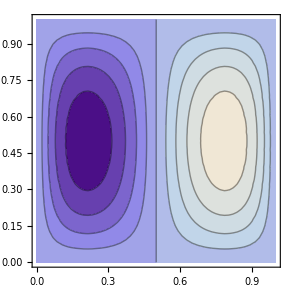

```mathematica
"curvas de nível da autofunção"
ContourPlot[ϕ[x,y],{x,0,a},{y,0,b}]
```